# Guard extraction soundness — Findings (v0)

## gtpyhop-diagnostics 0.1.0 → 0.1.1: which atoms explain_dead_end may name as blockers

type: findings
topic: diagnostics_guard_nnf
date: 2026-11-16
version: v0
prior-version: none
key-metric: unsound atoms over every guard tree of ≤ 7 nodes: 0 (prior: 28,833 with 0.1.0, delta: −28,833)
decision-required: confirm

## Headline Result

metric:    unsound atoms extracted, every guard expression tree of ≤ 7 nodes over 3 leaves, as a bail and as a wrapping guard
value:     0  (fix only, and fix + De Morgan split)
unit:      atoms
prior:     28,833 (0.1.0)
direction: down

decision-required is confirm, for one item: whether to keep commit 3948b54, the De Morgan split. Unlike the fix, it changes atoms that were already sound (making them finer), so it is kept as a separate commit that can be dropped. Everything else is informational.

## Model

An action guard yields a requirement: the test T itself for a wrapping guard or an else that bails, and not T for a bail (if T: return False). explain_dead_end names as blockers the atoms that evaluate false. That is honest only if every atom is necessary, that is implied by the requirement. The fix splits the requirement only where it is a conjunction, read through negation (its negation normal form):

syntax | requirement polarity | atoms | justification
not X | either | atoms of X, polarity flipped (kept as written if that splits nothing) | double negation
A and B and … | positive | atoms of each operand | a conjunction: each conjunct is necessary
A or B or … | negated | atoms of each operand, negated | De Morgan: not (A or B) = not A and not B
A and B | negated | kept whole | not (A and B) = not A or not B: neither is necessary alone
A or B | positive | kept whole | a disjunction: no side is necessary alone
anything else | either | kept whole | a leaf

Worked examples, extracted live by the three rules (A=p, B=q, C=r). An atom printed in red is unsound.

```mathematica
With[{cases={{"bail",and[p,q],True},{"bail",not[and[p,q]],True},{"bail",or[p,q],True},{"bail",and[p,or[q,r]],True},{"wrap",and[p,or[q,r]],False},{"wrap",and[not[or[p,q]],not[r]],False}}},tbl[{"guard","test","requirement","0.1.0","fix (185a327)","fix + De Morgan (3948b54)"},Table[With[{e=c⟦2⟧,neg=c⟦3⟧},{c⟦1⟧,show[e],ToString[BooleanMinimize[req[e,neg]],InputForm],Sequence@@(Row[Riffle[(If[T[req[e,neg]⇒lit[#1]],showAtom[#1],Style[showAtom[#1],Red]]&)/@#1,",  "]]&)/@{old[e,neg],cons[e,neg],nnf[e,neg]}}],{c,cases}]]]
```

guard | test | requirement | 0.1.0 | fix (185a327) | fix + De Morgan (3948b54)
bail | p && q |  !p ||  !q |  !p,   !q |  !(p && q) |  !(p && q)
bail |  !(p && q) | p && q | p,  q | p,  q | p,  q
bail | p || q |  !p &&  !q |  !(p || q) |  !(p || q) |  !p,   !q
bail | p && (q || r) |  !p || ( !q &&  !r) |  !p,   !(q || r) |  !(p && (q || r)) |  !(p && (q || r))
wrap | p && (q || r) | (p && q) || (p && r) | p,  q || r | p,  q || r | p,  q || r
wrap |  !(p || q) &&  !r |  !p &&  !q &&  !r |  !(p || q),   !r |  !(p || q),   !r |  !p,   !q,   !r

## Results Tables

### R1. The root cause and the table rows of the issue draft

```mathematica
tbl[{"claim","statement","result"},{{"L1 double negation","!!a ⟺ a",mark[T[!!p⧦p]]},{"L2 De Morgan (and)","!(a && b) ⟺ !a || !b",mark[T[!(p&&q)⧦!p||!q]]},{"L3 De Morgan (or)","!(a || b) ⟺ !a && !b",mark[T[!(p||q)⧦!p&&!q]]},{"L4 n-ary De Morgan","n = 1 … 10",mark[AllTrue[Range[10],With[{xs=Array[x,#1]},TautologyQ[!Or@@xs⧦And@@Not/@xs,xs]]&]]},{"root cause","!(a && b) ⟹ !a",mark[T[!(p&&q)⇒!p]]},{"  counterexample","",FindInstance[!(!(p&&q)⇒!p),{p,q},Booleans]},{"row 2: bail on a && b","no single literal of a, b is necessary",mark[NoneTrue[{p,!p,q,!q},T[!(p&&q)⇒#1]&]]},{"row 3: bail on a || b","!a and !b each necessary, jointly sufficient",mark[T[!(p||q)⇒!p]&&T[!(p||q)⇒!q]&&T[!p&&!q⧦!(p||q)]]},{"row 4: wrap a && (b || c)","b || c cannot be narrowed to b or c",mark[NoneTrue[{q,!q,r,!r},T[p&&(q||r)⇒#1]&]]}}]
```

claim | statement | result
L1 double negation | !!a ⟺ a | proved
L2 De Morgan (and) | !(a && b) ⟺ !a || !b | proved
L3 De Morgan (or) | !(a || b) ⟺ !a && !b | proved
L4 n-ary De Morgan | n = 1 … 10 | proved
root cause | !(a && b) ⟹ !a | fails
  counterexample |  | {{p→True,q→False}}
row 2: bail on a && b | no single literal of a, b is necessary | proved
row 3: bail on a || b | !a and !b each necessary, jointly sufficient | proved
row 4: wrap a && (b || c) | b || c cannot be narrowed to b or c | proved

The "fails" on the root-cause line is the defect: a bail on a conjunction does not require the negation of either conjunct. The counterexample is the reproduction's own state.

### R2. Proof for every expression, by induction on the syntax tree

Claim: for every test e and polarity, the conjunction of the extracted atoms is equivalent to the requirement. Each clause of the rule is shown to preserve this, assuming it for the children (IH: Ai ⟺ Ri). Equivalence then gives necessity of every atom by and-elimination.

```mathematica
With[{step=Function[{n,comb},With[{A=Array[Subscript[aa, #1]&,n],R=Array[Subscript[rr, #1]&,n]},TautologyQ[And@@MapThread[Equivalent,{A,R}]⇒And@@A⧦comb[R],Join[A,R]]]]},tbl[{"clause of the rule","obligation","result"},{{"not x, negated","req(not x, True) ⟺ req(x, False)",mark[TautologyQ[!!x⧦x,{x}]]},{"not x, positive","req(not x, False) ⟺ req(x, True)",mark[TautologyQ[!x⧦!x,{x}]]},{"and[v1..vn], positive","AND(atoms of children) ⟺ And(vi), n = 2 … 7",mark[AllTrue[Range[2,7],step[#1,And@@#1&]&]]},{"or[v1..vn], negated","AND(atoms of children, each req = !vi) ⟺ !Or(vi), n = 2 … 7",mark[AllTrue[Range[2,7],With[{V=Array[Subscript[vv, #1]&,#1],A=Array[Subscript[aa, #1]&,#1]},TautologyQ[And@@MapThread[Equivalent,{A,Not/@V}]⇒And@@A⧦!Or@@V,Join[A,V]]]&]]},{"kept whole","the single atom is the requirement",mark[True]},{"necessity","req ⟺ AND(atoms) ⟹ each atom, n = 1 … 7",mark[AllTrue[Range[7],With[{A=Array[Subscript[aa, #1]&,#1]},AllTrue[A,Function[ai,TautologyQ[And@@A⇒ai,A]]]]&]]},{"0.1.0's bail clause","AND(!a, !b) ⟺ !(a && b)",mark[T[!p&&!q⧦!(p&&q)]]}}]]
```

clause of the rule | obligation | result
not x, negated | req(not x, True) ⟺ req(x, False) | proved
not x, positive | req(not x, False) ⟺ req(x, True) | proved
and[v1..vn], positive | AND(atoms of children) ⟺ And(vi), n = 2 … 7 | proved
or[v1..vn], negated | AND(atoms of children, each req = !vi) ⟺ !Or(vi), n = 2 … 7 | proved
kept whole | the single atom is the requirement | proved
necessity | req ⟺ AND(atoms) ⟹ each atom, n = 1 … 7 | proved
0.1.0's bail clause | AND(!a, !b) ⟺ !(a && b) | fails

The fix-only rule (185a327) uses a subset of these clauses (it never splits under negation except through not), so the same argument covers it. 0.1.0 fails exactly at its bail clause.

### R3. Exhaustive cross-check

```mathematica
all=Join@@Table[ex2[n],{n,1,7}];Length[all]
```

24573

```mathematica
tbl[{"extractor","guards","atoms","unsound atoms","guards where AND(atoms) ≠ requirement","atoms not a sub-expression"},{Prepend[summ[old,all],"0.1.0"],Prepend[summ[cons,all],"fix (185a327)"],Prepend[summ[nnf,all],"fix + De Morgan (3948b54)"]}]
```

extractor | guards | atoms | unsound atoms | guards where AND(atoms) ≠ requirement | atoms not a sub-expression
0.1.0 | 49146 | 94947 | 28833 | 9951 | 0
fix (185a327) | 49146 | 73671 | 0 | 0 | 0
fix + De Morgan (3948b54) | 49146 | 101022 | 0 | 0 | 0

Every expression tree of up to 7 nodes over three leaves, binary and ternary and/or, each checked as a bail and as a wrapping guard over all 8 assignments.

### R4. Precision of the fix + De Morgan rule

An atom counts as imprecise when a strictly stronger literal inside it (a sub-expression or its negation) is necessary and is not already implied by the sibling atoms: a sounder, more specific blocker the rule does not name.

```mathematica
distinct=Select[all,DuplicateFreeQ[Cases[{#1},p|q|r,∞]]&];Length[distinct]
```

1869

```mathematica
tbl[{"expressions","atoms","imprecise atoms","share"},{({"all, ≤ 7 nodes",summ[nnf,all]⟦2⟧,#1,pct[#1/(summ[nnf,all]⟦2⟧)]}&)[imprecise[nnf,all]],({"no leaf repeated",summ[nnf,distinct]⟦2⟧,#1,pct[#1/(summ[nnf,distinct]⟦2⟧)]}&)[imprecise[nnf,distinct]]}]
```

expressions | atoms | imprecise atoms | share
all, ≤ 7 nodes | 101022 | 1536 | 1.52 %
no leaf repeated | 6510 | 0 | 0.0 %

```mathematica
{T[!r&&(r||q)⇒q],T[r||q⇒q],showAtom/@nnf[and[not[r],or[r,q]],False]}
```

{True,False,{ !r,r || q}}

The draft's example: the requirement implies q, but the atom (r || q) alone does not, so finding q takes reasoning across atoms.

### R5. The reported reproduction

p = state.locked_a[x] = True, q = state.locked_b[x] = False, r = (state.fuel[x] > 0) = False; guards: bail on p && q, bail on !r.

```mathematica
With[{s={p->True,q->False,r->False}},tbl[{"extractor","atoms named as blockers"},({#1⟦1⟧,Row[Riffle[showAtom/@Select[Join[#1⟦2⟧[and[p,q],True],#1⟦2⟧[not[r],True]],!(lit[#1]/.s)&],",  "]]}&)/@{{"0.1.0",old},{"fix (185a327)",cons},{"fix + De Morgan (3948b54)",nnf}}]]
```

extractor | atoms named as blockers
0.1.0 |  !p,  r
fix (185a327) | r
fix + De Morgan (3948b54) | r

### R6. The second source: control flow (not fixed)

Each shape's success condition is written from the code; the atoms are what the ast.walk extractor yields for it.

```mathematica
tbl[{"shape","success condition","extracted atoms","unsound atoms"},With[{rows={{"if a: if b: return False",!(p&&q),{!q}},{"if a: ...return s;  if b: ...return s",p||q,{p,q}},{"if a: return s;  if b: return False;  return s",p||!q,{p,!q}},{"if a: return False  elif b: return False",!p&&!q,{!p,!q}},{"if a: if b: return s",p&&q,{p,q}}}},({#1⟦1⟧,ToString[#1⟦2⟧,InputForm],ToString[#1⟦3⟧,InputForm],ToString[Select[#1⟦3⟧,Function[at,!T[#1⟦2⟧⇒at]]],InputForm]}&)/@rows]]
```

shape | success condition | extracted atoms | unsound atoms
if a: if b: return False |  !(p && q) | { !q} | { !q}
if a: ...return s;  if b: ...return s | p || q | {p, q} | {p, q}
if a: return s;  if b: return False;  return s | p ||  !q | {p,  !q} | {p,  !q}
if a: return False  elif b: return False |  !p &&  !q | { !p,  !q} | {}
if a: if b: return s | p && q | {p, q} | {}

```mathematica
tbl[{"launcher","bail fires (action blocked here)","atom launcher != 'mpirun' reported failed"},Table[{If[l===None,"None","'"<>l<>"'"],!!(l=!=None&&l=!="mpirun"),l=!="mpirun"},{l,{None,"mpirun","srun"}}]]
```

launcher | bail fires (action blocked here) | atom launcher != 'mpirun' reported failed
None | False | True
'mpirun' | False | False
'srun' | True | True

rikyu_hpc a_submit_job: if launcher is not None: if launcher != 'mpirun': return False. With launcher = None nothing blocks, yet the atom is reported as failed.

## Observations

Signal | Baseline / Expected | Observed [source] | Interpretation
unsound atoms | 0 for a correct extractor | 28,833 → 0 [R3] | the defect class is closed for every shape up to the bound, and for all sizes by R2
atoms ≠ requirement | 0 | 9,951 guards → 0 [R3] | no precondition is lost either: the atoms are exactly the requirement
atoms per guard | more atoms = finer blame | 73,671 (fix) → 101,022 (+ De Morgan) [R3] | the De Morgan commit only refines; it never adds an unsound atom
imprecise atoms | draft: 1.8 %, "mostly where a leaf repeats" | 1.5 %; 0 when no leaf repeats [R4] | the remaining gap is semantic (cross-atom), not syntactic
reproduction blockers | only the fuel guard | 0.1.0: !p, !r; both fixes: !r [R5] | the reported symptom is gone
control-flow shapes | atoms necessary | 3 of 5 shapes unsound [R6] | a second root cause, outside expression splitting

### Scope: what this does not prove

The counts from files (11 and 17 bundled actions, 408, 865 and 1,072 in the corpus, recognition 330 and 5,808, the 13/11 and 53/27 bounds) are measurements, made with the Python scripts in scripts/ next to this notebook.

The model is two-valued logic over the guard leaves. Python's truthiness agrees with it; a leaf that raises lands in unevaluated, which explain_dead_end never names as a blocker.

Diagnostics run after find_plan returns; none of this changes which plans are found.

## Charts & Visualizations

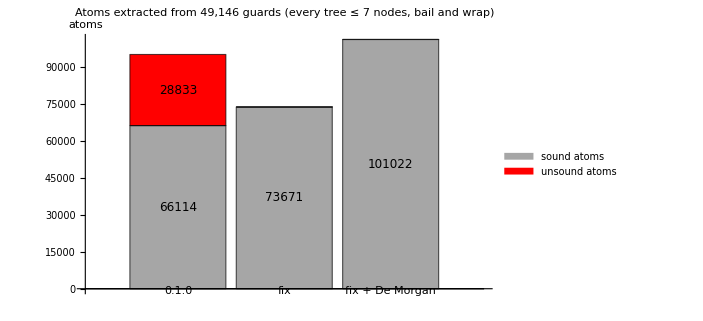

```mathematica
With[{d={summ[old,all],summ[cons,all],summ[nnf,all]}},BarChart[{{d⟦1,2⟧-d⟦1,3⟧,d⟦1,3⟧},{d⟦2,2⟧,0},{d⟦3,2⟧,0}},ChartLayout->"Stacked",ChartLabels->{{"0.1.0","fix","fix + De Morgan"},None},ChartLegends->Placed[{"sound atoms","unsound atoms"},Below],ChartStyle->{GrayLevel[0.65],Red},AxesLabel->{None,"atoms"},LabelingFunction->(If[#1>0,Placed[Style[#1,Black,12],Center],None]&),PlotLabel->"Atoms extracted from 49,146 guards (every tree ≤ 7 nodes, bail and wrap)",ImageSize->520]]
```

Caption: 0.1.0 extracts 28,833 unsound atoms (red); both fixes extract none, and the De Morgan split adds 27,351 sound atoms over the fix alone.

## Contradictions & Surprises

The precision gap is sharper than the draft said: it occurs only where a leaf repeats, never otherwise (R4).

A bundled example carries the second root cause: rikyu_hpc a_submit_job blames launcher != 'mpirun' when launcher is None (R6).

## Steering Questions

[now] Keep commit 3948b54 (De Morgan split)? It changes only sound atoms, making 17 bundled and 1,072 corpus actions finer.

[now] File the control-flow source as its own issue, with R6 as its evidence.

[next run] Path-aware extraction: drop, or conjoin with their path condition, the atoms of ifs not reached on every successful path.

[later] Refresh the README coverage claim: 285/293 predates collections added since; the current count is 330/335.

## Pointers

Commits 185a327 (fix), 3948b54 (De Morgan split), 1e63e38 (release gtpyhop-diagnostics 0.1.1)

tools/diagnostics_guard_check.py (8 cases, in checks.yml)

scripts/ next to this notebook: prop.py, examples_diff.py, corpus.py, cf.py (the measurements behind the counts)

## Appendix: definitions (initialization cells)

Inert syntax and[..], or[..], not[..] over leaves p, q, r, so that Wolfram does not simplify an expression before the rules see it. The notebook has its own context (CellContext -> Notebook), so a p, q or r defined elsewhere cannot leak into the leaves. nnf, cons and old mirror guards._requirement_atoms at 3948b54, at 185a327, and 0.1.0.

```mathematica
vars={p,q,r}
```

```mathematica
toB[e_]:=e/.{and->And,or->Or,not->Not}
```

```mathematica
req[e_,neg_]:=If[neg,!toB[e],toB[e]]
```

```mathematica
lit[{e_,neg_}]:=If[neg,!toB[e],toB[e]]
```

```mathematica
show[e_]:=ToString[toB[e],InputForm]
```

```mathematica
showAtom[at_]:=ToString[lit[at],InputForm]
```

```mathematica
nnf[not[x_],neg_]:=With[{in=nnf[x,!neg]},If[neg||Length[in]>1,in,{{not[x],neg}}]]
```

```mathematica
nnf[e_and,False]:=Join@@(nnf[#1,False]&)/@List@@e
```

```mathematica
nnf[e_or,True]:=Join@@(nnf[#1,True]&)/@List@@e
```

```mathematica
nnf[e_,neg_]:={{e,neg}}
```

```mathematica
cons[not[x_],True]:=cons[x,False]
```

```mathematica
cons[e_,True]:={{e,True}}
```

```mathematica
cons[e_and,False]:=Join@@(cons[#1,False]&)/@List@@e
```

```mathematica
cons[e_,False]:={{e,False}}
```

```mathematica
split[e_and]:=Join@@split/@List@@e
```

```mathematica
split[e_]:={e}
```

```mathematica
old[not[x_],True]:=({#1,False}&)/@split[x]
```

```mathematica
old[e_,True]:=({#1,True}&)/@split[e]
```

```mathematica
old[e_,False]:=({#1,False}&)/@split[e]
```

```mathematica
T[f_]:=TautologyQ[f,vars]
```

```mathematica
tt[f_]:=BooleanTable[f,vars]
```

```mathematica
check[rule_,e_,neg_]:=Module[{R=tt[req[e,neg]],ats=rule[e,neg],A},A=(tt[lit[#1]]&)/@ats;{Length[ats],Count[A,col_/;!And@@MapThread[Implies,{R,col}]],Boole[tt[And@@lit/@ats]=!=R],Boole[!AllTrue[ats,MemberQ[Level[{e},{0,∞},Heads->False],#1⟦1⟧]&]]}]
```

```mathematica
ex2[1]=vars
```

```mathematica
ex2[n_]:=ex2[n]=DeleteDuplicates[Join[not/@ex2[n-1],Join@@Table[Join@@({and@@#1,or@@#1}&)/@Tuples[{ex2[k],ex2[n-1-k]}],{k,1,n-2}],If[n≥4,Join@@Flatten[Table[Join@@({and@@#1,or@@#1}&)/@Tuples[{ex2[i],ex2[j],ex2[n-1-i-j]}],{i,1,n-3},{j,1,n-2-i}],1],{}]]]
```

```mathematica
summ[rule_,exprs_]:=summ[rule,exprs]=Module[{res=Flatten[Table[check[rule,e,neg],{e,exprs},{neg,{True,False}}],1]},{Length[res],Total[res⟦All,1⟧],Total[res⟦All,2⟧],Total[res⟦All,3⟧],Total[res⟦All,4⟧]}]
```

```mathematica
subs[e_]:=DeleteCases[DeleteDuplicates[Cases[{e},_and|_or|_not|p|q|r,{2,∞}]],e]
```

```mathematica
imprecise[rule_,exprs_]:=Module[{n=0},Do[Module[{ats=rule[e,neg],Rb=req[e,neg]},Do[Module[{ab=lit[at],ob=And@@lit/@DeleteCases[ats,at,{1},1]},If[AnyTrue[Join@@({toB[#1],!toB[#1]}&)/@subs[at⟦1⟧],Function[L,T[Rb⇒L]&&!T[ab⇒L]&&!T[ob⇒L]]],n++]],{at,ats}]],{e,exprs},{neg,{True,False}}];n]
```

```mathematica
tbl[headers_,rows_]:=Grid[Prepend[rows,(#1&)/@headers],Frame->All,Alignment->Left,Background->{None,{GrayLevel[0.9]}},Spacings->{1.2,0.6}]
```

```mathematica
pct[x_]:=TextString[N[Round[100 x,1/100]]]<>" %"
```

```mathematica
mark[b_]:=If[TrueQ[b],Style["proved",Darker[Green]],Style["fails",Red]]
```